```mathematica
integrand[ρ_]:=1/(√(1-1/ρ))
```

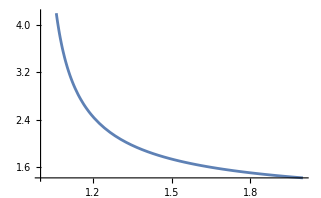

```mathematica
Plot[integrand[ρ],{ρ,1,2}]
```

Note that this integrand blows up at ρ=1. This is potentially severe trouble. But, let’s rewrite the integrand:

1/(√(1-1/ρ))=(√ρ)/(√(ρ-1))

Then notice that at the troublesome point, ρ=1, the numerator is completely reasonable and tends toward 1 as ρ tends toward 1. So without changing the nature of the singularity in the integrand, we’ll just replace the numerator by 1.

1/(√(ρ-1))

Let’s make another change of variables x=ρ-1. The lower limit of integration is now 0, and the upper limit is now 1. And the integrand is now just

1/(√x)

But everybody knows (he-he) that the integral of 1/(√x) is 2 √x. And this definite integral evaluated from 0 to 1 is just 2, because the lower limit is 0 and has no ill behavior despite the fact that the integrand blew up as 1/(√x). This is known as an integrable singularity. And the upshot is that there isn’t an infinite proper distance as we measure a radial path all the way down to r=2M.